```mathematica
δ[p_,q_,k1_]:=Subscript[δ, 0]+(Subscript[δ, 1]-Subscript[δ, 0])/(1+Exp[-k1*(p-q)]);
ρ[p_,k2_]:=Subscript[ρ, 0]+(Subscript[ρ, 1]-Subscript[ρ, 0])/(1+Exp[k2*p]);(* prey trait decreases growth and incresases prey protection by decreasing predator attack*)
μ[q_,k3_]:=Subscript[μ, 0]+(Subscript[μ, 1]-Subscript[μ, 0])/(1+Exp[-k3*q]);(* predqator trait increases natural mortality and incresases predator's succesful predation*)
```

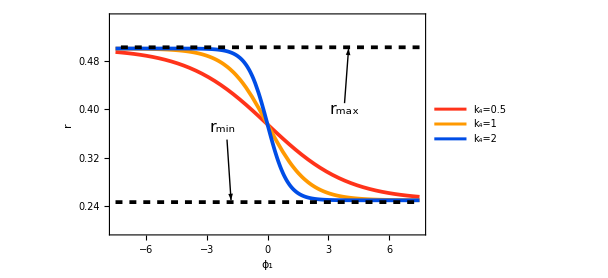

```mathematica
Subscript[ρ, 0]=0.25;Subscript[ρ, 1]=0.5;
i=Plot[{ρ[p,0.5],ρ[p,1], ρ[p,2]},{p,-7.5,7.5},PlotRange->{{-7.5,7.5},{0.2,0.55}},PlotStyle->{{RGBColor[1.0,0.2,0.1],Thickness[0.006]},(*Fiery Red-Orange*){RGBColor[1.0,0.6,0.0],Thickness[0.006]},(*Golden Orange*){RGBColor[0.0,0.3,0.9],Thickness[0.006]}    (*Deep Blue Contrast*)},PlotLegends->Placed[LineLegend[{"k_4=0.5","k_4=1","k_4=2"},LegendFunction->(Framed[#,Background->White,FrameStyle->Black]&),LegendLayout->"Column"],{0.13,0.25}],Axes->False,Frame->True,FrameLabel->{"ϕ_1","r"},LabelStyle->{FontSize->16},FrameStyle->Directive[Black,Thickness[0.003]],Epilog->{Inset[Style["r_max",16,Black],{3.8,0.4}],Inset[Style["r_min",16,Black],{-2.2,0.37}]},ImageSize->450];
j=ContourPlot[{{ρ==0.247},{ρ==0.502}},{p,-7.5,7.5},{ρ,0.2,0.55},ContourStyle->{{Black,Dashed,Thickness[0.006]}}];
j1=Graphics[{Arrow[{{3.8,0.41},{4,0.5}}](*,Arrow[{{2,0.87},{2,0.77}}]*)}];
j2=Graphics[{Arrow[{{-2,0.35},{-1.8,0.25}}](*,Arrow[{{2,0.87},{2,0.77}}]*)}];
s1=Show[i,j,j1,j2]
```

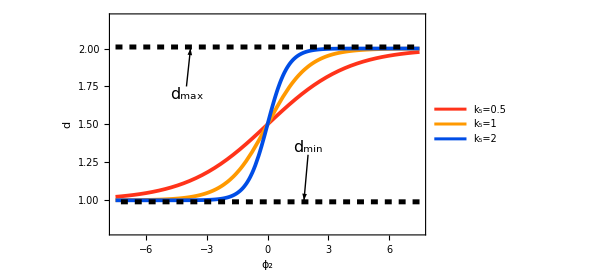

```mathematica
Subscript[μ, 0]=1;Subscript[μ, 1]=2;
i=Plot[{μ[p,0.5],μ[p,1], μ[p,2]},{p,-7.5,7.5},PlotRange->{{-7.5,7.5},{0.8,2.2}},PlotStyle->{{RGBColor[1.0,0.2,0.1],Thickness[0.006]},(*Fiery Red-Orange*){RGBColor[1.0,0.6,0.0],Thickness[0.006]},(*Golden Orange*){RGBColor[0.0,0.3,0.9],Thickness[0.006]}    (*Deep Blue Contrast*)},PlotLegends->Placed[LineLegend[{"k_5=0.5","k_5=1","k_5=2"},LegendFunction->(Framed[#,Background->White,FrameStyle->Black]&),LegendLayout->"Column"],{0.845,0.24}],Axes->False,Frame->True,FrameLabel->{"ϕ_2","d"},LabelStyle->{FontSize->16},FrameStyle->Directive[Black,Thickness[0.003]],Epilog->{Inset[Style["d_max",16,Black],{-4,1.7}],Inset[Style["d_min",16,Black],{2,1.35}]},ImageSize->450];
j=ContourPlot[{{μ==2.01},{μ==0.99}},{p,-7.5,7.5},{μ,0.9,2.1},ContourStyle->{{Black,Dashed,Thickness[0.008]}}];
j1=Graphics[{Arrow[{{2,1.3},{1.8,1}}]}];
j2=Graphics[{Arrow[{{-4,1.75},{-3.8,2}}]}];
s2=Show[i,j,j1,j2]
```

```mathematica
Subscript[δ, 0]=1;Subscript[δ, 1]=2;
s3=Plot3D[δ[p,q,0.5],{p,-5,5},{q,-5,5},Boxed->True,Mesh->{5,5},BoxStyle->Directive[Black,Bold,Thickness[0.003]],ColorFunction->"BrightBands",AxesLabel->{Subscript[ϕ, 1],Subscript[ϕ, 2],g},LabelStyle->{FontSize->16,Black},ImageSize->350,ViewPoint->{-2,-1,1}]
s4=Plot3D[δ[p,q,1.0],{p,-5,5},{q,-5,5},Boxed->True,Mesh->{5,5},BoxStyle->Directive[Black,Bold,Thickness[0.003]],ColorFunction->"BrightBands",AxesLabel->{Subscript[ϕ, 1],Subscript[ϕ, 2],g},LabelStyle->{FontSize->16,Black},ImageSize->350,ViewPoint->{-2,-1,1}]
s5=Plot3D[δ[p,q,2.0],{p,-5,5},{q,-5,5},Boxed->True,Mesh->{5,5},BoxStyle->Directive[Black,Bold,Thickness[0.003]],ColorFunction->"BrightBands",PlotLegends->BarLegend[{"BrightBands",{1,2}}],AxesLabel->{Subscript[ϕ, 1],Subscript[ϕ, 2],g},LabelStyle->{FontSize->16,Black},ImageSize->350,ViewPoint->{-2,-1,1}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
g1=Grid[{{Style["A",20],Style["B",20]},{s1,s2}},Alignment->Center,Spacings->{-0.1,- 0.65}]
g2=Grid[{{Style["C: k_6=0.5",20],Style["D: k_6=1.0",20],Style["E: k_6=2.0",20]},{s3,s4,s5}},Alignment->Center]
```

A | B
-Graphics- | -Graphics-

C: k_6=0.5 | D: k_6=1.0 | E: k_6=2.0
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
δ[p_,q_]:=Subscript[δ, 0]+(Subscript[δ, 1]-Subscript[δ, 0])/(1+Exp[-k1*(p-q)]);
ρ[p_]:=Subscript[ρ, 0]+(Subscript[ρ, 1]-Subscript[ρ, 0])/(1+Exp[-k2*p]);(* prey trait decreases growth and incresases prey protection by decreasing predator attack*)
μ[q_]:=Subscript[μ, 0]+(Subscript[μ, 1]-Subscript[μ, 0])/(1+Exp[k3*q]);(* predqator trait increases natural mortality and incresases predator's succesful predation*)
```

```mathematica
D[δ[p,q],{p,1}]
D[δ[p,q],{q,1}]
```

(ⅇ^(-k1 (p-q)) k1 (-δ_0+δ_1))/((1+ⅇ^(-k1 (p-q)))^2)

-(ⅇ^(-k1 (p-q)) k1 (-δ_0+δ_1))/((1+ⅇ^(-k1 (p-q)))^2)

```mathematica
D[δ[p,q],{p,1}]+D[δ[p,q],{q,1}]
```

0

```mathematica
D[δ[p,q],{p,2}]
D[δ[p,q],{q,2}]
```

((2 ⅇ^(-2 k1 (p-q)) k1^2)/((1+ⅇ^(-k1 (p-q)))^3)-(ⅇ^(-k1 (p-q)) k1^2)/((1+ⅇ^(-k1 (p-q)))^2)) (-δ_0+δ_1)

((2 ⅇ^(-2 k1 (p-q)) k1^2)/((1+ⅇ^(-k1 (p-q)))^3)-(ⅇ^(-k1 (p-q)) k1^2)/((1+ⅇ^(-k1 (p-q)))^2)) (-δ_0+δ_1)

```mathematica
D[δ[p,q],{p,2}]-D[δ[p,q],{q,2}]
```

0

```mathematica
ρ'[p]
ρ''[p]
```

(ⅇ^(-k2 p) k2 (-ρ_0+ρ_1))/((1+ⅇ^(-k2 p))^2)

(2 ⅇ^(-2 k2 p_) k2^2 (-ρ_0+ρ_1))/((1+ⅇ^(-k2 p_))^3)-(ⅇ^(-k2 p_) k2^2 (-ρ_0+ρ_1))/((1+ⅇ^(-k2 p_))^2)

```mathematica
μ'[q]
μ''[q]
```

-(ⅇ^(k3 q) k3 (-μ_0+μ_1))/((1+ⅇ^(k3 q))^2)

(2 ⅇ^(2 k3 q) k3^2 (-μ_0+μ_1))/((1+ⅇ^(k3 q))^3)-(ⅇ^(k3 q) k3^2 (-μ_0+μ_1))/((1+ⅇ^(k3 q))^2)